```mathematica
(*Зададим коэффициенты данного дифференциального уравнения*)
p[x_]=0;
q[x_]=1;
f[x_]=x;
(*Зададим отрезок, на котором ищется решение задачи*)
a=0;
b=Pi/2;
(*Зададим краевые условия*)
alpha0=1;
alpha1=0;
A=1;
beta0=1;
beta1=0;
B=Pi/2;
(*Решим первую вспомогательную задачу Коши для дифференцильного уравнения второго порядка методом сведения к решению системы обыкновенных дифференциальных уравнений*)
(*Зададим правые части системы дифференциальных уравнений, соответствующей данному дифференциальному уравнению второго порядка*)
f1[x_,y_,z_]=z;
f2[x_,y_,z_]=-p[x]*z-q[x]*y;
(*Зададим начальные условия для системы дифференциальных уравнений*)
x0=a;
U={-alpha1};
Z={alpha0};
(*Зададим количество частичных отрезков*)
n=20;
(*Найдем шаг разбиения*)
h=(b-x0)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[x0+k*h,{k,0,n}];
(*Реализуем алгоритм метода Эйлера для решения задачи Коши для систем обыкновенных дифференциальных уравнений*)
For[k=1,k≤n,k++,
AppendTo[U,U[[k]]+h*f1[X[[k]],U[[k]],Z[[k]]]];
AppendTo[Z,Z[[k]]+h*f2[X[[k]],U[[k]],Z[[k]]]]
];
(*Выполним интерполяцию найденного приближенного решения многочленом Лагранжа*)u[x_]=Sum[U[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Решим вторую вспомогательную задачу Коши для обыкновенного дифференциального уравнения второго порядкаметодом сведения к решению системы обыкновенных дифференциальных уравнений*)
(*Зададим правые части системы дифференциальных уравнений, соответствующей данному дифференциальному уравнению второго порядка*)
f1[x_,y_,z_]=z;
f2[x_,y_,z_]=f[x]-p[x]*z-q[x]*y;
(*Зададим начальные условия для системы дифференциальных уравнений*)
(*Зададим начальные условия для системы дифференциальных уравнений*)
If[alpha0!=0,
V={A/alpha0};Z={0},
V={0};Z={A/alpha1}];
(*Реализуем алгоритм метода Эйлера для решения задачи Коши для систем обыкновенных дифференциальных уравнений*)
For[k=1,k≤n,k++,
AppendTo[V,V[[k]]+h*f1[X[[k]],V[[k]],Z[[k]]]];
AppendTo[Z,Z[[k]]+h*f2[X[[k]],V[[k]],Z[[k]]]]
];
(*Выполним интерполяцию найденного приближенного решения многочленом Лагранжа*)v[x_]=Sum[V[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Найдем значение постоянной, входящей в представление решения исходной задачи методом редукции*)
u1[x_]=D[u[x],x];
v1[x_]=D[v[x],x];
Const=N[(B-beta0*v[b]-beta1*v1[b])/(beta0*u[b]+beta1*u1[b])];
(*Построим найденное решение*)
y[x_]=Const*u[x]+v[x];
GR=Plot[y[x],{x,a,b},PlotStyle->Red,PlotLegends->"Expressions"];
```

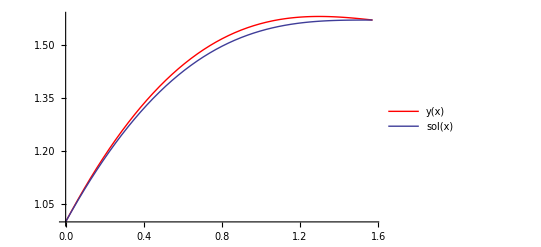

```mathematica
(*Найдем точное решение данной задачи, используя встроенные средства*)
Sol=DSolve[{s''[x]+p[x]*s'[x]+q[x]*s[x]==f[x],alpha0*s[a]+alpha1*s'[a]==A,beta0*s[b]+beta1*s'[b]==B},s[x],x];
sol[x_]=s[x]/.Sol[[1]];G=Plot[sol[x],{x,a,b},PlotLegends->"Expressions"];
(*Построим графики приближенного и точного решения*)
Show[GR,G]
```

```mathematica
r=NIntegrate[Abs[y[x]-sol[x]],{x,a,b}]
```

0.0215075